```mathematica
Clear["Global`*"]
```

# Unbalanced Lattice

## Constants

```mathematica
c = 299792458; (*m/s, Speed of Light in Vacuum*)
ℏ = 1.054571628*10^-34; (*J/s, Planck's constant*)
ϵ0 = 8.854187817*10^-12; (*F/m, Permittivity of Free Space*)
a0 = .529177*10^-10; (* Bohr radius, m *)
kB = 1.38*10^-23;

el = 1.602*10^-19;
AMU=1.66*10^-27*kg;
cm=10^-2;mm=10^-3;μm=10^-6;nm = 10^-9;pm=10^-12;fm=10^-15;
kg=1;g=10^-3;ng=10^-9*g;pg=10^-12*g;
Hz=1;kHz=10^3;MHz=10^6;GHz=10^9; THz = 10^12;
kK=1;mK=10^-3;μK=10^-6;nK=10^-9;
Ww=1;mW=10^-3;μW=10^-6;nW=10^-9;
Pa=1;GPa=10^9;
ms=10^-3;
ohm=1;V=1;mV=10^-3;
ns = 10^-9;

λ689 = 689*10^-9; (*m, in vacuum*)
λ698 = 698*10^-9; (*m, in vacuum*)
λ707 = 707*10^-9; (* m, in vacuum *)
λ813 = 813.4*10^-9; (*m, in vacuum*)
γ3p1 = 2π(7.5*10^3); (*rad/s, atom linewidth FWHM*)
γ3p0 = 2π(.001); (*rad/s, atom linewidth FWHM*)
γ461 = 32*10^6*2π;(*rad/s, atom linewidth FWHM*)
γ707  = 10*10^6*2π; (*NOT ACTUAL, USE FOR NOW*)
Isat461 = 42*10^-3*10^4; (* W/m^2*)
m = 87*1.66*10^-27; (* Sr 87, kg *)
α = 282*4π ϵ0 a0^3; (* dipole polarizability of ground, 3p0 at 813nm, from Boyd thesis *)
ωr = 4.7*1000*2π; (* recoil frequency clock trans ??? *)
```

```mathematica
λl =λ813 √2/2;
kl = (2Pi)/(2 λl);
Er = (ℏ kl)^2/(2m);
U=5Er;
J = 4/(√π)Er(U/Er)^(3/4)Exp[-2 √(U/Er)];
```

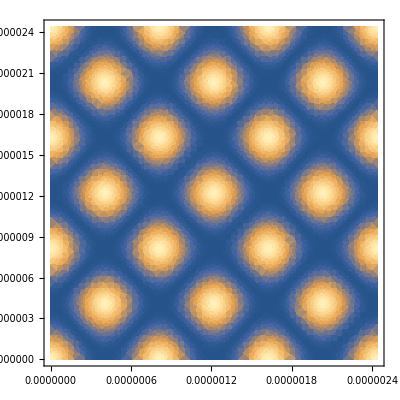

```mathematica
I0 = 1;
k = 2 π/λ813;
powertrans = 0.95;
loss2p  = powertrans;
Ef[x_,ϕ_]:=√I0 Exp[I (k x+ϕ)];
Uj[x_,y_]:=Abs[Ef[x,0]+loss2p^3 Ef[-x,0]+loss2p Ef[y,0]+loss2p^2 Ef[-y,0]]^2*U/(16J)
DensityPlot[Uj[x,y],{x,0,3λ813},{y,0,3λ813},MaxRecursion->3]
```

```mathematica
D[Uj[x,y,1,0,0,0,0],x]
```

7.25089 ((0.-7.72459×10^6 ⅈ) ⅇ^((0.-7.72459×10^6 ⅈ) x)+(0.+7.72459×10^6 ⅈ) ⅇ^((0.+7.72459×10^6 ⅈ) x)) Abs[ⅇ^((0.-7.72459×10^6 ⅈ) x)+ⅇ^((0.+7.72459×10^6 ⅈ) x)+ⅇ^((0.-7.72459×10^6 ⅈ) y)+ⅇ^((0.+7.72459×10^6 ⅈ) y)] Abs'[ⅇ^((0.-7.72459×10^6 ⅈ) x)+ⅇ^((0.+7.72459×10^6 ⅈ) x)+ⅇ^((0.-7.72459×10^6 ⅈ) y)+ⅇ^((0.+7.72459×10^6 ⅈ) y)]

```mathematica
Solve[D[Uj[x,y,.5,0,0,0,0],x]==0,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.+1.34599×10^-7 ⅈ}}

Independent phase control:

```mathematica
Ef[x_,ϕ_]:=√I0 Exp[I (k x+ϕ)];
Uj[x_,y_,loss_,ϕx_,ϕx2_,ϕy_,ϕy2_]:=Abs[Ef[x,ϕx]+loss^3 Ef[-x,ϕx2]+loss Ef[y,ϕy]+loss^2 Ef[-y,ϕy2]]^2*U/(16J);
Manipulate[DensityPlot[Uj[x,y, loss, ϕx,ϕx2,ϕy,ϕy2],{x,0,2λ813},{y,0,2λ813},PlotPoints->50],{{loss, 1, "Transmission"},0,1},{{ϕx, 0, "ϕx"},0,2π},{{ϕx2, 0, "ϕx2"},0,2π},{{ϕy, 0, "ϕy"},0,2π},{{ϕy2, 0, "ϕy2"},0,2π}]
```

DensityPlot::plln: Limiting value 2 λ813 in {x,0,2 λ813} is not a machine-sized real number.

Coupled phases:

```mathematica
Ef[x_,ϕ_]:=√I0 Exp[I (k x+ϕ)];
Uj[x_,y_,loss_,ϕ0_,ϕ1_]:=Abs[Ef[x,0]+loss^3 Ef[-x,ϕ0+ϕ1]+loss Ef[y,ϕ0]+loss^2 Ef[-y,ϕ1]]^2*U/(16J);
Manipulate[DensityPlot[Uj[x,y, loss, ϕ0,ϕ1],{x,0,2λ813},{y,0,2λ813},PlotPoints->50],{{loss, 1, "Transmission"},0,1},{{ϕ0, 0, "ϕ0"},0,2π},{{ϕ1, 0, "ϕ1"},0,2π}]
```

DensityPlot::plln: Limiting value 2 λ813 in {x,0,2 λ813} is not a machine-sized real number.

```mathematica
{xm,ym}={x,y}/.Solve[D[Uj[x,y,.5,0,0],x]==0&&D[Uj[x,y,.5,π/2,0],y]==0,{x,y}][[1]]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 6.49476×10^18+3123320157333639725 Log[ⅇ^((0.+1.54492×10^7 ⅈ) x)] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -6.49476×10^18+3123320157333639725 Log[ⅇ^((0.-1.54492×10^7 ⅈ) x)] == 0.

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is 3.24738×10^18+3123320157333639725 Log[ⅇ^((0.+7.72459×10^6 ⅈ) x)] == 0.

General::stop: Further output of Solve::incnst will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{0.+1.34599×10^-7 ⅈ,-1.01675×10^-7+4.48662×10^-8 ⅈ}

```mathematica
Manipulate[Plot[{Uj[x,x,trans,0,0],Uj[x,-x,trans,0,0]},{x,0,λ813 √2}],{{trans,1,"Transmission"},0,1}]
```

Plot::plln: Limiting value √2 λ813 in {x,0,√2 λ813} is not a machine-sized real number.

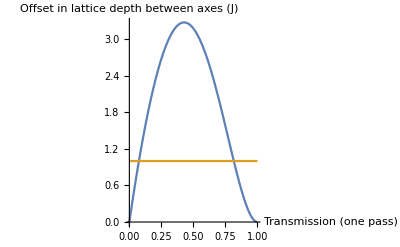

```mathematica
x=λ813/4;
Plot[{Uj[x,x,trans,0,0]-Uj[x,-x,trans,0,0],1},{trans,0,1},AxesLabel->{"Transmission (one pass)","Offset in lattice depth between axes (J)"}]
```